## Unstable oscillator with PD control (Problem 3.4)

```mathematica
Clear["Global`*"];
SetOptions[Plot,PlotRange -> All];
tmax=10;trange={t,0,tmax};d=DiracDelta[t]; (* d = input disturbance *)
G=1/(s^2-1); Gtf= TransferFunctionModel[G,s] ;   (* unstable undamped osc. *)
```

PD stabilization of an unstable oscillator; pole placement for critical damping at s = –1.

```mathematica
K1=Kp+ Kd s; Gyd1=Together[G/(1+K1 G)]//.{Kd->2 √(Kp-1),Kp->2}//Simplify;
Gud1=Together[(-K1 G)/(1+K1 G)]//.{Kd->2 √(Kp-1),Kp->2}//Simplify; {Gyd1,Gud1}
```

{1/(1+s)^2,-2/(1+s)}

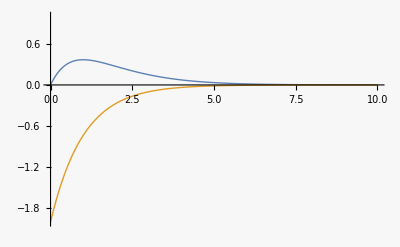

```mathematica
Gyd1tf=TransferFunctionModel[Gyd1,s];
y1=OutputResponse[Gyd1tf,d,trange];

Gud1tf=TransferFunctionModel[Gud1,s];
u1=OutputResponse[Gud1tf,d,trange];

p1=Plot[{y1,u1},{t,0,tmax},PlotRange->{-2,1}]
```

```mathematica
{OutputResponse[Gyd1tf,d,t],OutputResponse[Gud1tf,d,t]}//TraditionalForm
```

(ⅇ^-t t t
-2 ⅇ^-t t)

```mathematica
eqs1={y''[t]-y[t]==u[t]+d,u[t]==-Kp y[t]-Kd y'[t],y[0]==0,y'[0]==0}//.{Kd->2 √(Kp-1),Kp->2};
DSolveValue[eqs1,{y[t],u[t]},t]//Simplify//TraditionalForm
```

{ⅇ^-t t (t-0),2 ⅇ^-t (0-t)}

```mathematica
{ymax=Maximize[ⅇ^-t t ,t],ymax//N}
```

{{1/ⅇ,{t→1}},{0.367879,{t→1.}}}

Filtered PD control, with Kp, Kd, and ωd chosen to give 3 poles at s = –a.

```mathematica
K2=Kp+ (Kd s)/(1+s/ωd);Gyd2=Together[G/(1+K2 G)]//.{Kp->1+a^2/3,Kd->8/9 a,ωd->3a,a->1}//Simplify;
Gud2=Together[(-K2 G)/(1+K2 G)]//.{Kp->1+a^2/3,Kd->8/9 a,ωd->3a,a->1}//Simplify;
{Gyd2,Gud2}
```

{(3+s)/(1+s)^3,-4/(1+s)^2}

```mathematica
{Together[G/(1+K2 G)],Together[(-K2 G)/(1+K2 G)]}//Simplify
```

{(s+ωd)/(s^3+(-1+Kp) ωd+s^2 ωd+s (-1+Kp+Kd ωd)),-(Kd s ωd+Kp (s+ωd))/(s^3+(-1+Kp) ωd+s^2 ωd+s (-1+Kp+Kd ωd))}

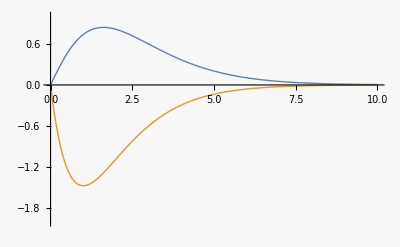

```mathematica
Gyd2tf=TransferFunctionModel[Gyd2,s];
y2=OutputResponse[Gyd2tf,d,trange];

Gud2tf=TransferFunctionModel[Gud2,s];
u2=OutputResponse[Gud2tf,d,trange];

p2=Plot[{y2,u2},{t,0,tmax},PlotRange->{-2,1}]
```

```mathematica
{OutputResponse[Gyd2tf,d,t],OutputResponse[Gud2tf,d,t]}//TraditionalForm
```

(3/2 ⅇ^-t t^2 t-1/2 ⅇ^-t (t-2) t t
-4 ⅇ^-t t t)

```mathematica
eqs2={y''[t]-y[t]==u[t]+d, 1/ωd u'[t]+ u[t]==-Kp y[t]-(Kp/ωd+Kd) y'[t],
y[0]==0,y'[0]==0,u[0]==0}//.{Kp->1+a^2/3,Kd->8/9 a,ωd->3a,a->1};
DSolveValue[eqs2,{y[t],u[t]},t]//Simplify//TraditionalForm
```

{-ⅇ^-t t (t+1) (0-t),4 ⅇ^-t t (0-t)}

```mathematica
{umin=Minimize[-4 ⅇ^-t t ,t],umin//N}
```

{{-4/ⅇ,{t→1}},{-1.47152,{t→1.}}}

```mathematica
{ymax2=Maximize[{t(t+1)ⅇ^-t  ,t>0},t],ymax2//N}
```

{{1/2 (1+√5) (1+1/2 (1+√5)) ⅇ^(1/2 (-1-√5)),{t→1/2 (1+√5)}},{0.839962,{t→1.61803}}}